# Ejemplo Series de Fourier

Se definen constantes y se gráfica la señal diente de sierra

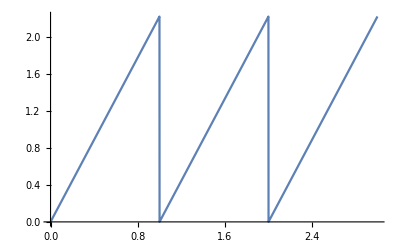

```mathematica
f=1;
ω0 = 2 π f;
T= 1/f;
V[t_]= π/(√2) SawtoothWave[f t];
Plot[{V[t]}, {t, 0, 3}]
```

En  el intervalo de 0 a T la señal diente de sierra se puede representar por :π/(√2)t .
Este ejemplo es para demostrar el uso del Lock-In SR830 y por eso se le da a la señal diente de sierra una amplitud pico a pico de π/(√2), para que la magnitud en RMS de la frecuencia fundamental sea 1/2.
A continuación se calcula la componente DC de la señal

```mathematica
dc = 2/T∫_0^T π/(√2)t ⅆt ;(*Se calcula el nivel dc de la señal*)
```

La función tabla permite hacer la integral para valores de n=1 hasta 10 y devuelve el resultado de cada integral en forma de arreglo.
A continuación se calculan los coeficientes de la serie de fourier para el seno.

```mathematica
Bn = Table[2/T∫_0^T π/(√2)t Sin[n ω0 t]ⅆt , {n, 1, 10}]
```

{-1/(√2),-1/(2 √2),-1/(3 √2),-1/(4 √2),-1/(5 √2),-1/(6 √2),-1/(7 √2),-1/(8 √2),-1/(9 √2),-1/(10 √2)}

```mathematica
An = Table[2/T∫_0^T t Cos[n ω0 t]ⅆt, {n, 1, 5}] (*calculo coeficientes de fourier del coseno*)
```

{0,0,0,0,0}

Se gráfica la señal diente de sierra original y su correspondiente serie de fourier para corroborar que los coeficientes obtenidos son los correctos.

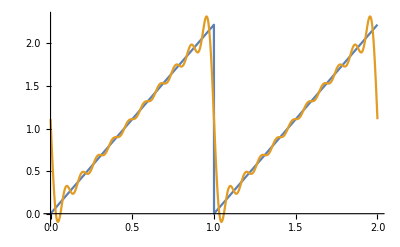

```mathematica
Plot[{V[t], dc/2 +∑_(n=1)^10 Bn[[n]]Sin[n ω0 t]}, {t, 0, 2}]
```

Los coeficientes obtenidos corresponden a la amplitud de la señal seno de cada fercuencia. Sin embargo el Lock-In mide en RMS. Entonces los coeficientes se pasan a valor RMS

```mathematica
Abs[Bn/(√2)]
```

{1/2,1/4,1/6,1/8,1/10,1/12,1/14,1/16,1/18,1/20}

```mathematica
N[π/(√2)] (*valor numerico aproximado de la amplitud pico a pico de la diente de sierra*)
```

2.22144

Se grafica en forma de tabla la magnitud RMS de cada uno de los coeficientes de la serie de fourier para una diente de sierra de amplitud pico a pico aproximadamente de 2.2 v.

```mathematica
Grid[{Prepend[Table[n, {n,1,10}] ,"f_n"], Prepend[Table[Abs[Bn[[n]]/(√2)], {n,1,10}] ,"A_n"]}, Frame->All, ItemStyle->"Large" , Spacings->{2, 2}]
```

f_n | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
A_n | 1/2 | 1/4 | 1/6 | 1/8 | 1/10 | 1/12 | 1/14 | 1/16 | 1/18 | 1/20